```mathematica
m=1.675*10^(-27);
k=1.381*10^(-23);
KE=0.025*1.602*10^(-19);
v0=Sqrt[(2*KE)/m];
n=(4*Pi*(v0^2))
```

6.00935×10^7

```mathematica
f[T_]:=((m/(2*Pi*k*T))^(3/2)) *Exp[(-1*m*(v0^2))/(2*k*T)]
```

```mathematica
h[T_]:=(2*Sqrt[KE/Pi])*((k*T)^(-(3/2)))*Exp[(-1*KE)/(k*T)]
```

```mathematica
DSolve[f'[T]==0,T]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

DSolve[-7.64506 ⅇ^(-290.007/T) (1/T)^(5/2)+1478.08 ⅇ^(-290.007/T) (1/T)^(7/2)==0,T]

```mathematica
D[h[T],T]
```

(4.03529×10^26 ⅇ^(-290.007/T))/T^(7/2)-(2.08717×10^24 ⅇ^(-290.007/T))/T^(5/2)

```mathematica
q[T_]:=(4.035288999574664*^26 ⅇ^(-290.00724112961615/T))/T^(7/2)-(2.0871663327388062*^24 ⅇ^(-290.00724112961615/T))/T^(5/2)
```

```mathematica
Solve[q[T]==0,T]
```

{{T→193.338}}

```mathematica
Plot[h[T],{T,0,500}]
```

-Graphics-

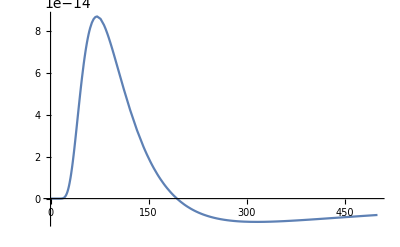

```mathematica
Plot[g[T],{T,0,500}]
```

```mathematica
f[T]
```

```mathematica
g[T_]:=-1.2721934513679106*^-7 ⅇ^(-290.00724112961615/T) (1/T)^(5/2)+0.000024596354200958148 ⅇ^(-290.00724112961615/T) (1/T)^(7/2)
```

```mathematica
Manipulate[f[T],{T,0,500}]
```

```mathematica
Manipulate[g[T],{T,0,500}]
```

```mathematica
0.00072076816999357 √(1/pi)
```

```mathematica
N[0.00072076816999357 √(1/pi)]
```

0.000720768 √(1/pi)

```mathematica
√(1/pi)
```

√(1/pi)

```mathematica
-7.64505694139878 (1/T)^(5/2)+1478.0812479025878  (1/T)^(7/2)
```

```mathematica
v0
```

2186.8

```mathematica
f[290]
```

0.000379653